```mathematica
ClearAll["Global`*"]
```

## Random Testing:

```mathematica
A=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HydrogenXS.csv"]
```

{{Energy,Total,Ps,Direct,Ann,Excitation ,Process,Threshold},{0.01,13.2033,0,0,0.0000996,0,Ps,6.8},{0.02,11.8169,0,0,0.0000704,0,Dir,13.6},1567,{4990,0.0999,0,0.0248,1.41×10^-7,0.0000212,,},{5000,0.0997,0,0.0248,1.41×10^-7,0,,}}
 |  |  |  |

```mathematica
Tot=A[[2;;1567,2]];
Elas = A[[2;;1567,2]]-A[[2;;1567,3]]-A[[2;;1567,4]]-A[[2;;1567,5]]-A[[2;;1567,6]];
```

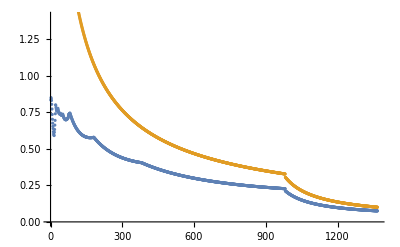

```mathematica
bs=ListPlot[{Elas[[200;;All]],Tot[[200;;All]]}]
```

```mathematica
Fit[Elas[[200;;All]],{1,x},x]
```

0.111892-0.0000728525 x

0.707289-0.000826235 x+2.77406×10^-7 x^2

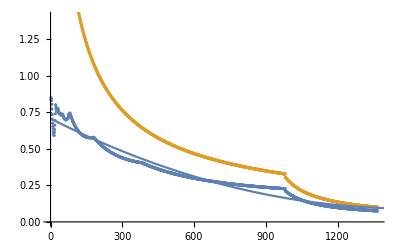

```mathematica
as=Fit[Elas[[200;;All]],{1,x,x*x},x]
Plot[as,{x,0,1500}];
Show[bs,%]
```

-5.38236+6.1651 ⅇ^(-x/1000)+0.00463219 x-1.33061×10^-6 x^2

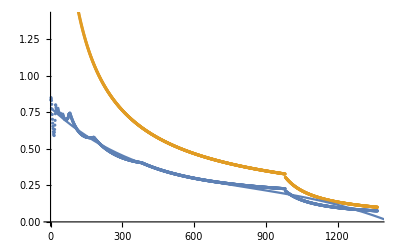

```mathematica
as=Fit[Elas[[200;;All]],{1,x,x*x,Exp[-x/1000]},x]
Plot[as,{x,0,1500}];
Show[bs,%]
```

{{v→                                 8
InterpolatingFunction[{{1., 1. 10 }}, <>]}}

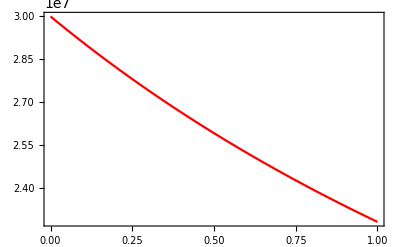

```mathematica
α = 3.5*^7;
β = 1/2000;
σ[x_] :=.6*^-20;
Subscript[v, 0] = 3*10^7;
Subscript[v, m] = 800;
range = 10^8;

Needs["DifferentialEquations`NDSolveUtilities`"];

sol=NDSolve[{v'[t]== -α * σ[v[t]]*v[t]^2*(β - Subscript[v, m]^2/v[t]^2),v[0]==Subscript[v, 0]},v,{t,1,range}]
Plot[Evaluate[v[t]/.sol], {t, 1, range}, 
PlotStyle -> {Red}, Axes -> False, Frame -> True]
```

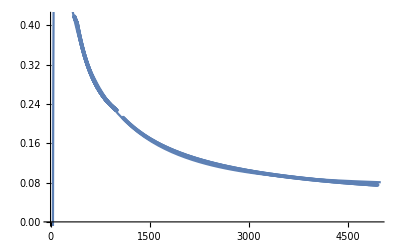

0.0644953+0.241011 ⅇ^(-x/1000)+73.5579/(0.1+x)-3132.55/(0.3+x)^2

```mathematica
A=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HydrogenXS.csv"];
Tot=A[[2;;1567,2]];
Energy = A[[2;;1567,1]];
Elas = A[[2;;1567,2]]-A[[2;;1567,3]]-A[[2;;1567,4]]-A[[2;;1567,5]]-A[[2;;1567,6]];


data=Thread[{Energy,Elas}][[270;;All]];
fit=Fit[data,{1,1/(x+.1),1/(x+.3)^2,Exp[-x/1000]},x];
Plot[fit,{x,0,5000}];
Show[{ListPlot[data[[270;;All]]],%}]
fit
```

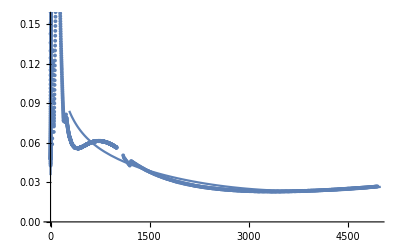

0.04717-0.000015591 x+2.16885×10^-9 x^2-17.0461/(10+x)^2+15.8749/(100+x)

```mathematica
A=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HeliumXS.csv"];
Tot=A[[2;;1567,2]];
Energy = A[[2;;1567,1]];
Elas = A[[2;;1567,2]]-A[[2;;1567,3]]-A[[2;;1567,4]]-A[[2;;1567,5]]-A[[2;;1567,6]];

Cutoff= 20;
data=Thread[{Energy,Elas}][[Cutoff;;All]];
fit=Fit[data,{1,1/(x+100),x/1000,x*x/10000,1/(x+10)^2},x];
Plot[fit,{x,0,5000}];
Show[{ListPlot[Thread[{Energy,Elas}][[1;;All]]],%}]
fit
```

## Hydrogen:

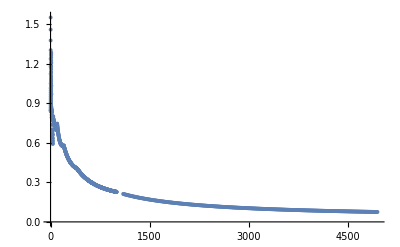

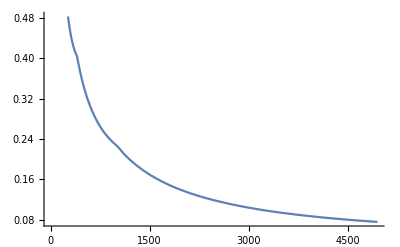

{{v→                                 8
InterpolatingFunction[{{1., 1. 10 }}, <>]}}

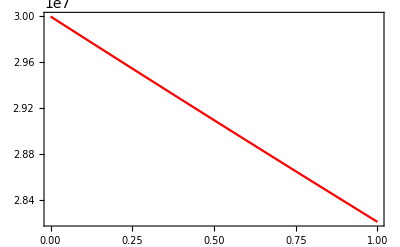

```mathematica
A=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HydrogenXS.csv"];
Tot=A[[2;;1567,2]];
Energy = A[[2;;1567,1]];
Elas = A[[2;;1567,2]]-A[[2;;1567,3]]-A[[2;;1567,4]]-A[[2;;1567,5]]-A[[2;;1567,6]];
data=Thread[{Energy,Elas}];
f=Interpolation[data];
ListPlot[data]
Plot[f[x],{x,0.01,4950}]
α = 3.5*^7;
β = 1/2000;
σ[x_] :=f[2.8437499999999995*^-12 x^2]*10^-20;
Subscript[v, 0] = 3*10^7;
Subscript[v, m] = 800;
range = 10^8;

Needs["DifferentialEquations`NDSolveUtilities`"];

sol=NDSolve[{v'[t]== -α * σ[v[t]]*v[t]^2*(β - Subscript[v, m]^2/v[t]^2),v[0]==Subscript[v, 0]},v,{t,1,range}]
Plot[Evaluate[v[t]/.sol], {t, 1, range}, 
PlotStyle -> {Red}, Axes -> False, Frame -> True]
```

## Helium:

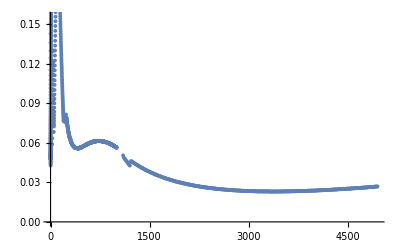

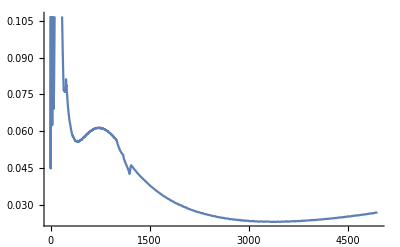

{{v→                                 8
InterpolatingFunction[{{1., 1. 10 }}, <>]}}

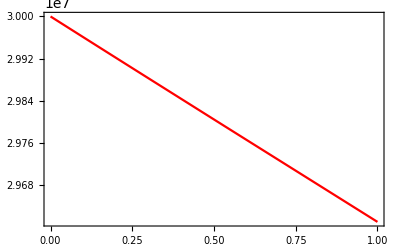

```mathematica
A=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HeliumXS.csv"];
Tot=A[[2;;1567,2]];
Energy = A[[2;;1567,1]];
Elas = A[[2;;1567,2]]-A[[2;;1567,3]]-A[[2;;1567,4]]-A[[2;;1567,5]]-A[[2;;1567,6]];
data=Thread[{Energy,Elas}];
f=Interpolation[data,InterpolationOrder->2];
ListPlot[data]
Plot[f[x],{x,0.01,4950}]


α = 3.5*^7;
β = 1/2000;
σ[x_] :=f[2.8437499999999995*^-12 x^2]*10^-20;
Subscript[v, 0] = 3*10^7;
Subscript[v, m] = 800;
range = 10^8;

Needs["DifferentialEquations`NDSolveUtilities`"];

sol=NDSolve[{v'[t]== -α * σ[v[t]]*v[t]^2*(β - Subscript[v, m]^2/v[t]^2),v[0]==Subscript[v, 0]},v,{t,1,range}]
Plot[Evaluate[v[t]/.sol], {t, 1, range}, 
PlotStyle -> {Red}, Axes -> False, Frame -> True]
```

## Scatter Plot:

```mathematica
A=ReadList["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\data.txt",Number,RecordLists->True];

Show[ListPointPlot3D[A,BoxRatios->{1, 1, 1}],
ContourPlot3D[x^2+y^2+z^2==(2*.048*3.08*10^16)^2,{x,-5*10^15,5*10^15},{y,-5*10^15,5*10^15},{z,-5*10^15,5*10^15}],ImageSize -> Large]
```

-Graphics3D-

## Rough Work:

## Definition of surge functions:(Piecewise thing not working at all)

```mathematica
xth = 1;
λ = 1;
ESurge[x_]:=Piecewise[{0,x<xth},{Exp[1]/λ*(x-xth)*Exp[(-(x-xth))/λ],x≥xth}]
LSurge[x_]:=Piecewise[{0,x<xth},{4*λ*(x-xth)/(x-xth+λ)^2,x≥xth}]
```

## Extraction of data and threading to make all cross_sections vs. Energy:

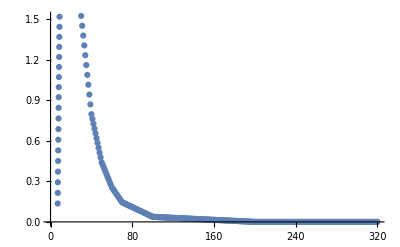

```mathematica
Data=Import["C:\\Users\\Himanshu\\Desktop\\Julia\\Base code for positron transport\\HydrogenXS.csv"];
TOT=Data[[2;;1567,2]];
EN= Data[[2;;1567,1]];
PS = Data[[2;;1567,3]];
ION = Data[[2;;1567,4]];
EX = Data[[2;;1567,6]];
Tot = Thread[{EN,TOT}];
Ps = Thread[{EN,PS}];
Ion = Thread[{EN,ION}];
Ex = Thread[{EN,EX}];
Elas = Data[[2;;1567,2]]-Data[[2;;1567,3]]-Data[[2;;1567,4]]-Data[[2;;1567,5]]-Data[[2;;1567,6]];
Elas=Thread[{EN,Elas}];
ListPlot[{Ps[[160;;500]]}]
```

## Trying out fitting and plotting (Not working):

```mathematica
start = 160;
end = 500;
λguess  =1;
xthguess = 10;
ClearAll[xth,λ]
fit=FindFit[Ps[[start;;end]],(x-xth)/λ*Exp[-(x-xth)/λ],{{λ,λguess},{xth,xthguess}},x,MaxIterations->1000]

ListPlot[{Ps[[start;;end]],Table[(Exp[1]*(x-xth)/λ*Exp[-(x-xth)/λ])/.fit,{x,EN[[start]],EN[[end]]}]}]
```

## Just simple plotting of surge functions vs. data:

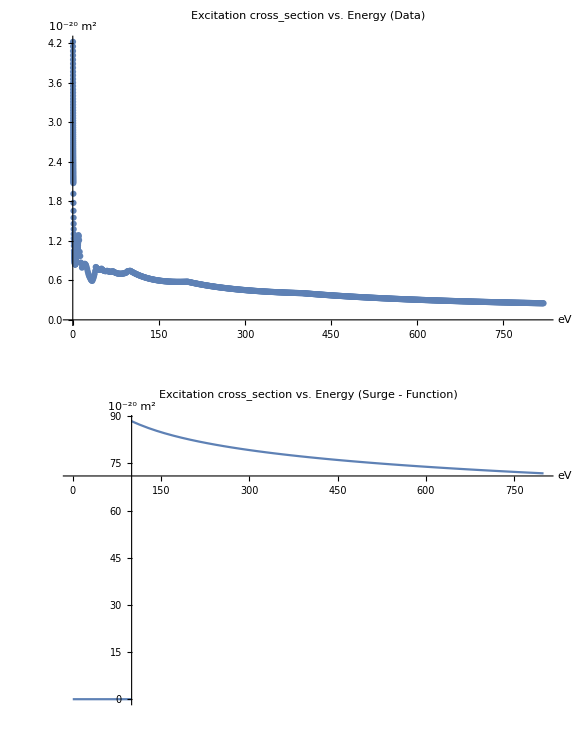

```mathematica
λ = 1;
xth = 100;
a=1/3;
start = 40;
end = 1000;

label = "Excitation cross_section vs. Energy (Surge - Function)";
label2 = "Excitation cross_section vs. Energy (Data)";

GraphicsColumn[{ListPlot[Elas[[start;;end]],PlotRange->All,PlotLabel->label2,AxesLabel->{eV,"10^-20 m^2"}],Show[{Plot[(a*Exp[1]/λ*(x-xth)*Exp[(-(x-xth))/λ])*0+320*.438/x^(.1),{x,xth,800},PlotRange->All,PlotLabel->label,AxesLabel->{eV,"10^-20 m^2"}],Plot[0*x,{x,0,xth}]}]},ImageSize->Large]
Export["C:\\Users\\Himanshu\\Desktop\\Ex44s.png",%,"PNG"]
```

## Rough @ 2

```mathematica
Elas;
```

{aa→22.7275,b→0.672958}

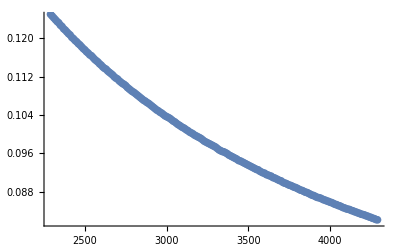

{aa→22.7275,b→0.672958}

```mathematica
start = 1300;
end = 1500;
λguess  =1;
xthguess = 10;
ClearAll[xth,λ]
fit=FindFit[Elas[[start;;end]],aa/x^(b),{aa,b},x]
Show[Plot[aa/x^b/.fit,{x,EN[[start]],EN[[end]]}],ListPlot[Elas[[start;;end]]]]
```

```mathematica
FindFit[Elas[[start;;end]],aa/x^(b),{aa,b},x]
```

{aa→20.9506,b→0.6598}

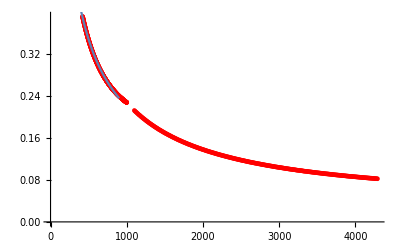

```mathematica
Show[ListPlot[Elas⟦start;;end⟧,PlotStyle->Red],Plot[aa/x^b/.{aa->20.950578613156395,b->0.6598004665823245},{x,1,901}]]
```